```mathematica
f=List@@(CountryData["World","Polygon"][[1]]);
```

```mathematica
(*multiply vectors on the left, as per Mathematica Lists, so 3x2 pair of perp vectors. If not down 001, then take 001 to be vertical, that is, final row is 0A. *)
Clear[projmatrixdownaxis];
projmatrixdownaxis[{0,0,1}]:={{1,0},{0,1},{0,0}};
projmatrixdownaxis[{a_,b_,c_}]:=projmatrixdownaxis[a,b,c]=
{{-b/(√(a^2+b^2)),-(a c)/(√(a^2+b^2) √(a^2+b^2+c^2))},{a/(√(a^2+b^2)),-(b c)/(√(a^2+b^2) √(a^2+b^2+c^2))},{0,(√(a^2+b^2))/(√(a^2+b^2+c^2))}};
```

```mathematica
latlong2space[{lat_,long_}]:={Cos[long Pi/180]Cos[lat Pi/180],Sin[long Pi/180]Cos[lat Pi/180],Sin[lat Pi/180]};
```

```mathematica
latlong2plane[axis_][{lat_,long_}]:=Module[{f,q},
q=long Pi/180;f=lat Pi/180;
{Cos[q]Cos[f],Sin[q]Cos[f],Sin[f]}.projmatrixdownaxis[axis]]
```

```mathematica
thinpath[path_,res_:.01]:=(*can miss necks*)
Module[{(*cp,lp,d,thin,resq*)},
thin = {path[[1]]};resq = res^2; Table[If[(#.#>resq)&@(thin[[-1]]-path[[k]]),AppendTo[thin,path[[k]]]],{k,2,Length[path]}];
If[Length[thin]<=2,{},AppendTo[thin,path[[1]]]]]
```

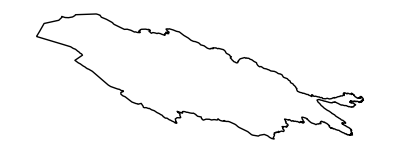

```mathematica
Graphics[Line[latlong2plane[{1,.2,.2}]/@f[[1,1]]],AspectRatio->Automatic]
```

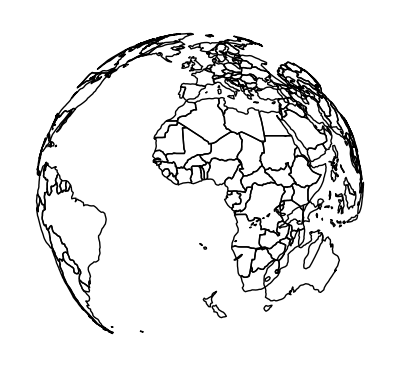

```mathematica
Graphics[Line[thinpath[latlong2plane[{1,0,0}][#]&/@#,.01]]&/@f[[1]]]
```

```mathematica
GeoGraphics[GeoRange->"World",GeoProjection->"LambertAzimuthal"]
```

-Graphics-

```mathematica
Clear[unwrappedsphere];
unwrappedsphere[s_?(0<#<=1 &)]:=unwrappedsphere[s]=  (*at 1, s is fully a sphere;0 is flat disk*)
Pi/s{Sin[s u]Cos[v],Sin[s u]Sin[v],-Cos[s u]+1}
```

```mathematica
Show[{Table[ParametricPlot3D[unwrappedsphere[s]/.{u->uu,v->vv},{uu,0,Pi},{vv,0,2Pi-.001},Mesh->False],{s,.8,0,-.8 (.999)/3}],
Table[ParametricPlot3D[unwrappedsphere[s]/.{u->Pi,v->vv},{vv,0,2Pi-.001},Mesh->False],{s,.8,0,-.8 (.999)/3}]},PlotRange->All,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
unwrappedsphere[1]
```

{ComplexInfinity,ComplexInfinity,ComplexInfinity}